```mathematica
(*参数设置*)
Clear[r,θ];
a=2;k=1;(*引力距离阶数&耦合系数*)
L=1/2(r'[t]^2+r[t]^2 θ'[t]^2)+k/r[t]^a;
```

```mathematica
(*生成演化方程*)
eq1=D[L,θ[t]]==D[D[L,θ'[t]],t];
eq2=D[L,r[t]]==D[D[L,r'[t]],t];
```

```mathematica
b=1;          (*初始截距*)
theta=0; (*初始角度*)
vn=0;       (*初始径向速度*)
vt=1.5;    (*初始法向速度*)
```

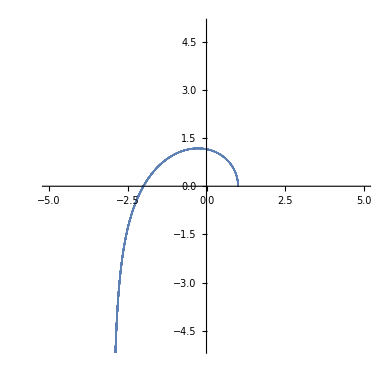

```mathematica
sol=NDSolve[{
eq1,
eq2,
r[0]==b,       
θ[0]==theta,       
r'[0]==vn,  
θ'[0]==vt/b   
},{r,θ},{t,0,100}];

(*赋值*)
rt=r/.sol[[1]];
θt=θ/.sol[[1]];
(*画图*)
data=Table[{rt[t]*Cos[θt[t]],rt[t]*Sin[θt[t]]},{t,0,100,0.001}];
ListPlot[data,AspectRatio->1,PlotRange->{{-5,5},{-5,5}}]
```